# 2. domača naloga

## 1. naloga

V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. Primer:
	d = Daljica[{-1, 1}, {3, -1}]

Sestavi naslednje funkcije:

```mathematica
d = Daljica[{-1, 1}, {3, -1}]
d1 = Daljica[{-1, 1}, {0, -1}]
d2 = Daljica[{0, 0}, {3, 1}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,1},{0,-1}]

Daljica[{0,0},{3,1}]

• Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB - AA]
```

```mathematica
Dolzina[d]
Dolzina[d1]
Dolzina[d2]
```

2 √5

√5

√10

• EnacbaNosilke[Daljica[AA_, BB_]], ki rne enačbo premice nosilke daljice. Primer, za daljico d kot zgoraj je enačba nosilke y == -x/2 + 1/2.

```mathematica
EnacbaNosilke[Daljica[AA_, BB_]] := Module[{x1, y1, x2, y2, k, n},
	{x1, y1} = AA;
	{x2, y2} = BB;
	k = (y1 - y2) / (x1 - x2);
	n = n/.First[Solve[y1 == k * x1 + n, n]];
	y == k * x + n]
```

```mathematica
EnacbaNosilke[d]
EnacbaNosilke[d1]
EnacbaNosilke[d2]
```

y==1/2-x/2

y==-1-2 x

y==x/3

• Slika[Daljica[AA_, BB_]], ki vrne graﬁčni objekt Line, kateri predstavlja daljico.

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
Slika[d1]
Slika[d2]
```

Line[{{-1,1},{3,-1}}]

Line[{{-1,1},{0,-1}}]

Line[{{0,0},{3,1}}]

• Narisi[d__Daljica], ki za eno ali več podanih daljic le-te izriše.

```mathematica
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

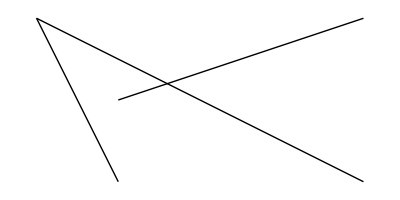

```mathematica
Narisi[d, d1, d2]
```

## 2. naloga

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_, BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r (BB - AA) == CC + s (DD - CC)}, {r, s}];
	If [resitev == {}, {}, First[AA + r (BB - AA)/. resitev]]]
```

```mathematica
Presek[d, d1]
Presek[d, d2]
Presek[d1, d2]
```

{-1,1}

{3/5,1/5}

{-3/7,-1/7}

## 3. naloga

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. Primer
	m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}]
Ker gre za sklenjen mnogokotnik, predvidevamo, da ima ta povezave med zaporednimi točkami ter od zadnje do prve točke. Sestavi naslednje funkcije:

• Slika[Mnogokotnik[t__]], ki predstavi mnogokotnik s pomočjo graﬁčnega objekta Line. Najprej sestavi nov seznam točk, ki vključuje obstoječe točke mnogokotnika ter še ponovljeno prvo. Pozor: pazi, da ne izbrišeš obstoječe funkcije za sliko daljice!

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3},{-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

• Narisi[m__Mnogokotnik],ki nariše enega ali več mnogokotnikov. Pazi, pri risanju moraš narediti tudi daljico od zadnje do začetne točke. Premisli, kako iz obstoječega seznama točk sestaviš nov seznam, ki daljši za eno točko, t.j. ponovljeno prvo točko (Namig: funkciji Append ter First na seznamih.)

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Map[Slika, Module[{seznam},
seznam =Append[{Last[m], First[m]}, m]]]]
```

```mathematica
Narisi[m1]
```

-Graphics-

• PravilniNKotnik[n_, r_], ki nariše pravilni n-kotnik s središčem v točki (0,0) in s točkami na krožnici z radijem r, pri čemer je ena točka v (r,0). Namig: uporabi funkcijo Table in upoštevaj, da se točke nahajajo na koordinatah (rcos(2π∗i n ,rsin(2π∗i n )) za i =0,...,n−1. Izriši 
	p5 = PravilniNKotnik[5, 2]

```mathematica
PravilniNKotnik[n_, r_] := Graphics[Polygon[Table[{r * Cos[2* Pi * i / n], r * Sin[2 * Pi * i / n]}, {i, 0, n-1}] ]]
```

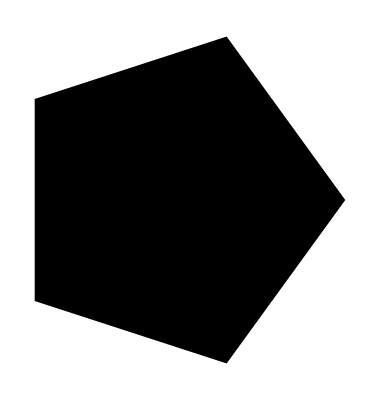

```mathematica
p5=PravilniNKotnik[5,2]
```

• Nadgradi prejšnjo funkcijo v PravilniNKotnik[n_, r_, phi_], ki zgornji pravilni n-kotnik zavrti za kot phi. Premisli, kako je treba nadgraditi formulo za posamezno točko, da se premakne za kot phi. Rezultat uporabi v kombinaciji s funkcijo Manipulate in interaktivno demonstriraj rotacijo.

```mathematica
PravilniNKotnik[n_, r_, phi_] := Graphics[Polygon[Table[{r * Cos[(phi + 2* Pi * i )/ n], r * Sin[(phi + 2 * Pi * i) / n]}, {i, 0, n-1}] ]]
```

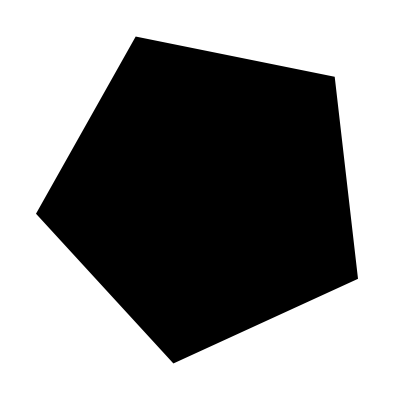

```mathematica
PravilniNKotnik[5, 1, 10]
```

```mathematica
Manipulate[PravilniNKotnik[n, r, phi] , {r, 0, 10}, {n, 1, 50}, {phi, 0, 360}]
```

• Daljice[Mnogokotnik[t__]], ki vrne seznam daljic, ki tvorijo mnogokotnik. Uporabi funkcijo Partition. V dokumentaciji preveri, kako deluje funkcija ter kako se uporablja zamikanje. Oglej si, kaj naredita naslednja ukaza:
	Partition[{1, 2, 3, 4, 5} , 2]
	Partition[{1, 2, 3, 4, 5} , 2, 1]

```mathematica
Partition[{1, 2, 3, 4, 5} , 2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
Daljice[Mnogokotnik[t__]] := Partition[Append[t, First[t]], 2, 1]
```

```mathematica
Daljice[m1]
```

First::argt: First called with 4 arguments; 1 or 2 arguments are expected.

Append::argt: Append called with 5 arguments; 1 or 2 arguments are expected.

Append::argt: Append called with 4 arguments; 1 or 2 arguments are expected.

Append[{0,0,{1,1}},{1,1,{0,3}},{0,3,{-1,2}},{-1,2,First[{0,0},{1,1},{0,3},{-1,2}]}]

## 4. naloga

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice. Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne istih presečišč večkrat. Poskusi uporabiti vgrajeni funkciji Select in DeleteDuplicates. Pomagaj si z naslednjimi primeri. Funkcijo lahko deﬁniramo tudi na naslednji način (namesto argumenta damo znak #, na koncu deﬁnicije pa dodamo znak &.
	aliJePrazen = Length[#] > 0 &
Primer uporabe:
	aliJePrazen[{}]
		False
	aliJePrazen[{1, 2, 3}]
		True
Potem jo pa lahko uporabimo kot preizkusno funkcijo za ﬁltriranje neustreznih praznih seznamov:
	Select[{{1, 2}, {}, {3, 4}, {}}, aliJePrazen]
		{{1, 2}, {3, 4}}

```mathematica
aliJePrazen = Length[#] > 0 &
```

Length[#1]>0&

```mathematica
Presek[m_Mnogokotnik, d_Daljica] := DeleteDuplicates[Select[Presek[Daljice[Mnogokotnik[m]], d, aliJePrazen]]]
```

## 5. naloga

Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.
	VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
	VsiPari[f, {1, 2, 3}, {a, b}]
		{f[1, a], f[1, b], f[2, a], f[2, b], f[3, a], f[3, b]}

• Preuči, kaj točno naredita funkciji Outer in Flatten. Poglej v pomoč in preizkusi na primerih.

```mathematica
Outer[f,{a,b},{x,y,z}]
Outer[Times, {2, 4, 6}, {a, b, c, e}]
Outer[Sqrt, {1, 2, 3, a, b}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

{{2 a,2 b,2 c,2 e},{4 a,4 b,4 c,4 e},{6 a,6 b,6 c,6 e}}

{1,√2,√3,√a,√b}

```mathematica
Flatten[{{a,b},{c,{j},e},{f,{g,h}}}]
Flatten[{{1, 2, 3}, {1}, {a, {b}, {a, c}}, {1, 3, 6, {{7}}}}]
```

{a,b,c,j,e,f,g,h}

{1,2,3,1,a,b,a,c,1,3,6,7}

• Sestavi funkcijo Presek[m1_Mnogokotnik, m2_Mnogokotnik], ki poišče presek dveh pravokotnikov. Uporabi funkcijo VsiPari.

```mathematica
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik] := VsiPari[Presek, m1, m2]
```

## 6. naloga

Izberi eno izmed nalog iz snovi pri linearni algebri in jo reši. Opiši potek in čim več računskega dela prepusti Mathematici. Če je možno, rezultate predstavi še graﬁčno.

Dana je matrika
	A = (-4 | 1 | 3 | 0
-2 | 7 | 1 | -1
1 | -1 | 9 | -3
-1 | 0 | 5 | -10).
Reši enačbo
	2 * A - X + I = 0.

```mathematica
a={{-4,1,3,0},{-2,7,1,-1},{1,-1,9,-3},{-1,0,5,-10}};
X=Array[x,{4,4}]
resitev1=Solve[2 a-X+IdentityMatrix[4]==Array[0&,{4,4}],Flatten[X]]
X/.Flatten[resitev1]//MatrixForm
```

{{x[1,1],x[1,2],x[1,3],x[1,4]},{x[2,1],x[2,2],x[2,3],x[2,4]},{x[3,1],x[3,2],x[3,3],x[3,4]},{x[4,1],x[4,2],x[4,3],x[4,4]}}

{{x[1,1]→-7,x[1,2]→2,x[1,3]→6,x[1,4]→0,x[2,1]→-4,x[2,2]→15,x[2,3]→2,x[2,4]→-2,x[3,1]→2,x[3,2]→-2,x[3,3]→19,x[3,4]→-6,x[4,1]→-2,x[4,2]→0,x[4,3]→10,x[4,4]→-19}}

(-7 | 2 | 6 | 0
-4 | 15 | 2 | -2
2 | -2 | 19 | -6
-2 | 0 | 10 | -19)

Rezultat:
	X = (-7 | 2 | 6 | 0
-4 | 15 | 2 | -2
2 | -2 | 19 | -6
-2 | 0 | 10 | -19)